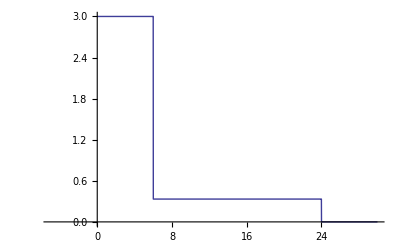

```mathematica
Clear[f]
f[x_]:=∞/;x<0
f[x_]:=3/;0<x<6
f[x_]:=1/3/;6<x<24
f[x_]:=0/;24<x<∞
Plot[f[x],{x,-5,30}]
```

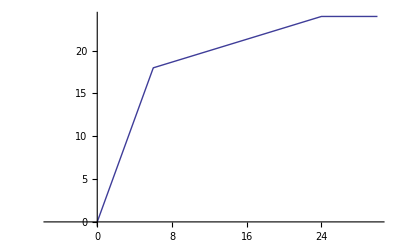

```mathematica
z[x_]:=3*x/;0<x<6
z[x_]:=x/3+16/;6<x<24
z[x_]:=24/;24<x<∞
Plot[z[x],{x,-5,30}]
```